#### Input Cvoigt, output a lattice diagram as well as the closest XISO as T_XISO and Cvoigt_XISO Evaluate common_funs.nb and ES_FindSymGroups.nb before running this notebook.

```mathematica
xeps=10^-7;
reps=0.1;
```

#### Igel (1995, Geophysics)

```mathematica
CmatIgel=({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
CmatIgel==Transpose[CmatIgel]
```

True

```mathematica
CmatIgelXISOmsat=({{9.6730, 2.6077, 2.8305, -0.1210, -0.1869, -0.4260}, {2.6077, 8.4039, 1.0912, 0.1360, 0.2310, 0.9131}, {2.8305, 1.0912, 7.8645, 0.1570, 0.4624, 0.6675}, {-0.1210, 0.1360, 0.1570, 3.5198, 0.1597, 0.0082}, {-0.1869, 0.2310, 0.4624, 0.1597, 3.9358, -0.1967}, {-0.4260, 0.9131, 0.6675, 0.0082, -0.1967, 3.5737}});
CmatIgelXISOmsat==Transpose[CmatIgelXISOmsat]
TmatIgelXISOmsat = Simplify[TmatOfCmat[CmatIgelXISOmsat]];
```

True

```mathematica
CmatIgelXISOvdb=({{9.7300, 2.2092, 2.0165, -0.6482, -0.6781, -0.5848}, {2.2092, 8.4402, 1.8344, 0.4718, 0.1912, 1.1227}, {2.0165, 1.8344, 8.7097, 0.4344, 1.1988, 0.0759}, {-0.6482, 0.4718, 0.4344, 3.2473, 0.1319, 0.2561}, {-0.6781, 0.1912, 1.1988, 0.1319, 3.5635, -0.6247}, {-0.5848, 1.1227, 0.0759, 0.2561, -0.6247, 3.7492}});
CmatIgelXISOvdb==Transpose[CmatIgelXISOvdb]
TmatIgelXISOvdb = Simplify[TmatOfCmat[CmatIgelXISOvdb]];
```

True

#### Russell et al. (1999, JGR)

```mathematica
CmatRussell=({{271.6149, 101.6837, 101.2700, 0, 0, -0.1902}, {101.6837, 233.9946, 99.9429, 0, 0, 0.3918}, {101.2700, 99.9429, 239.5542, 0, 0, 0.0071}, {0, 0, 0, 66.1769, 0.0452, 0}, {0, 0, 0, 0.0452, 74.6177, 0}, {-0.1902, 0.3918, 0.0071, 0, 0, 71.9655}});
CmatRussell==Transpose[CmatRussell]
```

True

#### Choose one

```mathematica
Cmat = CmatIgel; 
(* Cmat = CmatRussell; *)
```

#### Convert from Voigt to BB

```mathematica
Tmat = Simplify[TmatOfCmat[Cmat]];
Print["A given Voigt matrix is ",MatrixForm[Cmat]];  
Print["The corresponding [T]_𝔹𝔹 is ",MatrixForm[Tmat]];
```

A given Voigt matrix is (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.525
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.525 | -1. | 3.)

The corresponding [T]_𝔹𝔹 is (10. | 0.7 | 1.05 | 5.2 | -3.92598 | -3.10269
0.7 | 8. | -2. | -0.2 | -0.46188 | 0.326599
1.05 | -2. | 6. | -0.45 | -0.190526 | 0.318434
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22474
-3.92598 | -0.46188 | -0.190526 | 0. | 5.5 | 2.12132
-3.10269 | 0.326599 | 0.318434 | -1.22474 | 2.12132 | 13.)

#### Find closest elastic maps to each symmetry class

```mathematica
OutputFor[Tmat,MONO]
OutputFor[Tmat,ORTH]
OutputFor[Tmat,TET]
OutputFor[Tmat,CUBE]
OutputFor[Tmat,XISO]
OutputFor[Tmat,TRIG]
OutputFor[Tmat,ISO]
```

5-18-2023 8:51

NMinimize = {1.77381,{θ→3.09621,ϕ→1.55544}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_MONO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {177.4,0.,89.1})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0153358 | -0.0453676 | -0.998853
0.000696467 | -0.99897 | 0.0453622
-0.999882 | 0 | 0.0153516)  (minimizes the function  U ⟶ d(T, 𝒱_MONO(U)))

𝒱_MONO(U_0)contains a closest map to T in 𝒯_MONO

d(T, 𝒯_MONO) = 1.774 (Distance from T to 𝒯_MONO)

β_MONO^T = 0.075 = 4.31^o (Angle betweem T and 𝒯_MONO)

P(T, 𝒱_MONO(U_0)) = (10.0483 | 0.312292 | 0.626973 | 5.21023 | -3.95328 | -3.07084
0.312292 | 7.96402 | -1.96673 | 0.37924 | -0.115107 | -0.213739
0.626973 | -1.96673 | 6.07884 | 0.0499997 | -0.114125 | -0.15424
5.21023 | 0.37924 | 0.0499997 | 5.39035 | 0.00319104 | -1.17338
-3.95328 | -0.115107 | -0.114125 | 0.00319104 | 5.5185 | 2.10692
-3.07084 | -0.213739 | -0.15424 | -1.17338 | 2.10692 | 13.)  (a closest elastic map to T having symmetry at least MONO)

5-18-2023 8:51

NMinimize = {2.87693,{θ→1.50411,σ→1.59241,ϕ→0.745272}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_ORTH(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,91.2,42.7})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.998603 | -0.0273918 | 0.0451902
0.0507699 | -0.734539 | 0.676665
0.0146589 | 0.678013 | 0.734903)  (minimizes the function  U ⟶ d(T, 𝒱_ORTH(U)))

𝒱_ORTH(U_0)contains a closest map to T in 𝒯_ORTH

d(T, 𝒯_ORTH) = 2.877 (Distance from T to 𝒯_ORTH)

β_ORTH^T = 0.122 = 6.99^o (Angle betweem T and 𝒯_ORTH)

P(T, 𝒱_ORTH(U_0)) = (10.1157 | 0.364344 | 0.689551 | 5.37884 | -3.57156 | -3.14724
0.364344 | 6.88009 | -1.8658 | 0.446441 | -0.16058 | -0.216482
0.689551 | -1.8658 | 7.16022 | -0.11541 | -0.127861 | -0.215284
5.37884 | 0.446441 | -0.11541 | 4.97391 | -0.259338 | -1.65581
-3.57156 | -0.16058 | -0.127861 | -0.259338 | 5.87004 | 1.25698
-3.14724 | -0.216482 | -0.215284 | -1.65581 | 1.25698 | 13.)  (a closest elastic map to T having symmetry at least ORTH)

5-18-2023 8:51

NMinimize = {3.35528,{θ→1.4968,σ→0.0253455,ϕ→0.738956}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TET(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {85.8,1.5,42.3})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0293571 | -0.998328 | 0.0497941
0.738786 | 0.0552263 | 0.671673
-0.6733 | 0.0170688 | 0.739172)  (minimizes the function  U ⟶ d(T, 𝒱_TET(U)))

𝒱_TET(U_0)contains a closest map to T in 𝒯_TET

d(T, 𝒯_TET) = 3.355 (Distance from T to 𝒯_TET)

β_TET^T = 0.142 = 8.16^o (Angle betweem T and 𝒯_TET)

P(T, 𝒱_TET(U_0)) = (11.1309 | 0.448615 | 0.697439 | 4.76643 | -3.41665 | -3.25279
0.448615 | 6.9373 | -1.77937 | 0.414542 | -0.146851 | -0.241143
0.697439 | -1.77937 | 7.23219 | -0.229555 | -0.0991671 | -0.219123
4.76643 | 0.414542 | -0.229555 | 4.1546 | 0.124873 | -1.46976
-3.41665 | -0.146851 | -0.0991671 | 0.124873 | 5.545 | 1.20878
-3.25279 | -0.241143 | -0.219123 | -1.46976 | 1.20878 | 13.)  (a closest elastic map to T having symmetry at least TET)

5-18-2023 8:52

NMinimize = {8.23431,{θ→1.49874,σ→0.810614,ϕ→0.774284}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_CUBE(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {85.9,46.4,44.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.687363 | -0.724568 | 0.0503407
0.543518 | -0.467157 | 0.69739
-0.481789 | 0.506721 | 0.714922)  (minimizes the function  U ⟶ d(T, 𝒱_CUBE(U)))

𝒱_CUBE(U_0)contains a closest map to T in 𝒯_CUBE

d(T, 𝒯_CUBE) = 8.234 (Distance from T to 𝒯_CUBE)

β_CUBE^T = 0.356 = 20.4^o (Angle betweem T and 𝒯_CUBE)

P(T, 𝒱_CUBE(U_0)) = (9.76453 | 0.28951 | 0.562001 | 2.87489 | -1.84227 | 0
0.28951 | 7.73056 | -3.93852 | 0.56992 | -0.013716 | 0
0.562001 | -3.93852 | 7.88398 | -0.165233 | -0.250723 | 0
2.87489 | 0.56992 | -0.165233 | 5.24225 | -0.880738 | 0
-1.84227 | -0.013716 | -0.250723 | -0.880738 | 4.37868 | 0
0 | 0 | 0 | 0 | 0 | 13.)  (a closest elastic map to T having symmetry at least CUBE)

5-18-2023 8:52

NMinimize = {6.50485,{θ→1.50483,ϕ→0.714334}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,0.,40.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0 | 0.75553)  (minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

𝒱_XISO(U_0)contains a closest map to T in 𝒯_XISO

d(T, 𝒯_XISO) = 6.505 (Distance from T to 𝒯_XISO)

β_XISO^T = 0.279 = 15.98^o (Angle betweem T and 𝒯_XISO)

P(T, 𝒱_XISO(U_0)) = (12.0284 | 0.456493 | 0.397549 | 3.07421 | -2.91164 | -3.27377
0.456493 | 5.14803 | 0.181413 | 0.182489 | -0.192338 | -0.216259
0.397549 | 0.181413 | 5.09532 | 0.166797 | -0.150985 | -0.187109
3.07421 | 0.182489 | 0.166797 | 6.33018 | -1.13784 | -1.41006
-2.91164 | -0.192338 | -0.150985 | -1.13784 | 6.39812 | 1.36334
-3.27377 | -0.216259 | -0.187109 | -1.41006 | 1.36334 | 13.)  (a closest elastic map to T having symmetry at least XISO)

5-18-2023 8:52

NMinimize = {6.0697,{θ→4.65869,σ→-0.107489,ϕ→2.47124}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_TRIG(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {266.9,-6.2,141.6})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (-0.0653149 | 0.997307 | -0.0333426
0.783718 | 0.0305863 | -0.620363
-0.617673 | -0.0666501 | -0.783606)  (minimizes the function  U ⟶ d(T, 𝒱_TRIG(U)))

𝒱_TRIG(U_0)contains a closest map to T in 𝒯_TRIG

d(T, 𝒯_TRIG) = 6.07 (Distance from T to 𝒯_TRIG)

β_TRIG^T = 0.26 = 14.89^o (Angle betweem T and 𝒯_TRIG)

P(T, 𝒱_TRIG(U_0)) = (11.4507 | 0.487067 | 0.34218 | 2.65889 | -3.93072 | -3.27232
0.487067 | 6.39207 | -0.0866282 | 0.0188249 | 0.109346 | -0.175877
0.34218 | -0.0866282 | 3.85189 | -0.0149055 | -0.243399 | -0.139238
2.65889 | 0.0188249 | -0.0149055 | 7.09059 | -0.535507 | -1.29157
-3.93072 | 0.109346 | -0.243399 | -0.535507 | 6.21472 | 1.63641
-3.27232 | -0.175877 | -0.139238 | -1.29157 | 1.63641 | 13.)  (a closest elastic map to T having symmetry at least TRIG)

5-18-2023 8:52

𝒱_ISO(U) = 𝒱_ISO(I), independent of U, so the function U ⟶ d(T, 𝒱_ISO(U)) = d(T, 𝒯_ISO) is constant.

d(T, 𝒯_ISO) = 12.0102   (Distance from T to 𝒯_ISO)

β_ISO^(□  T) = 0.533 = 30.55^o (Angle betweem T and 𝒯_ISO

P(T,𝒱_ISO(I)) = (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)  (The closest elastic map to T having symmetry ISO)

Lamé parameters for P(T,𝒱_ISO(I)) are λ = 2. and μ = 3.5, Poisson is 0.181818

#### Lattice diagram

ChopT = 0.01^o

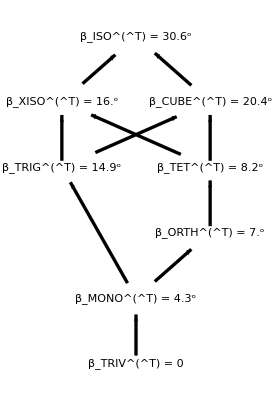

```mathematica
LatticeOfDTs[Tmat]
```

### Closest maps The ordering here follows BC2004: TRIV-MONO-ORTH-TET-XISO-ISO, with CUB and TRIG (not considered in BC2004) added at the end.

```mathematica
TmatTRIV =closest[1]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,MONO],TRIV],xeps];
TmatMONO =closest[2]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,MONO],MONO],xeps];
TmatORTH =closest[3]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,ORTH],ORTH],xeps];
TmatTET   =closest[4]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,TET],TET],xeps];
TmatXISO =closest[5]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,XISO],XISO],xeps];
TmatISO   =closest[6]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,ISO],ISO],xeps];
TmatCUBE =closest[7]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,CUBE],CUBE],xeps];
TmatTRIG =closest[8]=Chop[ProjToVSigOfU[Tmat,UT[Tmat,TRIG],TRIG],xeps];
```

```mathematica
table=Table[Table[Round[AngleMatrix[closest[i],closest[j]]/Degree,.01],{i,8}],{j,8}]
```

{{0.,4.31,6.99,8.16,15.98,30.55,20.4,14.89},{4.31,0.,5.53,6.99,15.41,30.28,19.97,14.46},{6.99,5.53,0.,4.28,14.64,29.82,19.34,15.74},{8.16,6.99,4.28,0.,13.96,29.54,18.96,15.31},{15.98,15.41,14.64,13.96,0.,26.39,24.55,7.04},{30.55,30.28,29.82,29.54,26.39,0.,23.25,26.99},{20.4,19.97,19.34,18.96,24.55,23.25,0.,25.3},{14.89,14.46,15.74,15.31,7.04,26.99,25.3,0.}}

```mathematica
TableForm[Join[{{TRIV,MONO,ORTH,TET,XISO,ISO,CUBE,TRIG}},table],TableSpacing->{5,2}]
```

TRIV | MONO | ORTH | TET | XISO | ISO | CUBE | TRIG
0. | 4.31 | 6.99 | 8.16 | 15.98 | 30.55 | 20.4 | 14.89
4.31 | 0. | 5.53 | 6.99 | 15.41 | 30.28 | 19.97 | 14.46
6.99 | 5.53 | 0. | 4.28 | 14.64 | 29.82 | 19.34 | 15.74
8.16 | 6.99 | 4.28 | 0. | 13.96 | 29.54 | 18.96 | 15.31
15.98 | 15.41 | 14.64 | 13.96 | 0. | 26.39 | 24.55 | 7.04
30.55 | 30.28 | 29.82 | 29.54 | 26.39 | 0. | 23.25 | 26.99
20.4 | 19.97 | 19.34 | 18.96 | 24.55 | 23.25 | 0. | 25.3
14.89 | 14.46 | 15.74 | 15.31 | 7.04 | 26.99 | 25.3 | 0.

### Checks on angles listed in the lattice

```mathematica
Print["beta(T,MONO) = ",(Round[AngleMatrix[Tmat,TmatMONO] /Degree,reps])^o];
Print["beta(T,ORTH) = ",(Round[AngleMatrix[Tmat,TmatORTH] /Degree,reps])^o];
Print["beta(T,TET) = ",(Round[AngleMatrix[Tmat,TmatTET] /Degree,reps])^o];
Print["beta(T,CUBE) = ",(Round[AngleMatrix[Tmat,TmatCUBE] /Degree,reps])^o];
Print["beta(T,TRIG) = ",(Round[AngleMatrix[Tmat,TmatTRIG] /Degree,reps])^o];
Print["beta(T,XISO) = ",(Round[AngleMatrix[Tmat,TmatXISO] /Degree,reps])^o];
Print["beta(T,ISO) = ",(Round[AngleMatrix[Tmat,TmatISO] /Degree,reps])^o];
```

beta(T,MONO) = 4.3^o

beta(T,ORTH) = 7.^o

beta(T,TET) = 8.2^o

beta(T,CUBE) = 20.4^o

beta(T,TRIG) = 14.9^o

beta(T,XISO) = 16.^o

beta(T,ISO) = 30.6^o

### Angles between adjacent maps in the lattice

```mathematica
(* right side path *)
Print["beta(T,MONO) = ",(Round[AngleMatrix[Tmat,TmatMONO] /Degree,reps])^o];
Print["beta(MONO,ORTH) = ",(Round[AngleMatrix[TmatMONO,TmatORTH] /Degree,reps])^o];
Print["beta(ORTH,TET) = ",(Round[AngleMatrix[TmatORTH,TmatTET] /Degree,reps])^o];
Print["beta(TET,CUBE) = ",(Round[AngleMatrix[TmatTET,TmatCUBE] /Degree,reps])^o];
Print["beta(CUBE,ISO) = ",(Round[AngleMatrix[TmatCUBE,TmatISO] /Degree,reps])^o];
(* left side path *)
Print["beta(MONO,TRIG) = ",(Round[AngleMatrix[TmatMONO,TmatTRIG] /Degree,reps])^o];
Print["beta(TRIG,XISO) = ",(Round[AngleMatrix[TmatTRIG,TmatXISO] /Degree,reps])^o];
Print["beta(XISO,ISO) = ",(Round[AngleMatrix[TmatXISO,TmatISO] /Degree,reps])^o];
(* cross segments *)
Print["beta(TET,XISO) = ",(Round[AngleMatrix[TmatTET,TmatXISO] /Degree,reps])^o];
Print["beta(TRIG,CUBE) = ",(Round[AngleMatrix[TmatTRIG,TmatCUBE] /Degree,reps])^o];
```

beta(T,MONO) = 4.3^o

beta(MONO,ORTH) = 5.5^o

beta(ORTH,TET) = 4.3^o

beta(TET,CUBE) = 19.^o

beta(CUBE,ISO) = 23.3^o

beta(MONO,TRIG) = 14.5^o

beta(TRIG,XISO) = 7.^o

beta(XISO,ISO) = 26.4^o

beta(TET,XISO) = 14.^o

beta(TRIG,CUBE) = 25.3^o

### Closest XISO

#### Double-check that TmatXISO is indeed XISO

```mathematica
TmatXISO =Chop[ProjToVSigOfU[Tmat,UT[Tmat,XISO],XISO],xeps];
OutputFor[TmatXISO,XISO]
```

5-18-2023 11:11

NMinimize = {2.82709×10^-8,{θ→1.50483,ϕ→0.714334}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {86.2,0.,40.9})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.0498003 | -0.997825 | 0.0431815
0.753887 | 0.0659144 | 0.65369
-0.655115 | 0 | 0.75553)  (minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

𝒱_XISO(U_0) contains T

d(T, 𝒯_XISO) = 2.83×10^-8 (Distance from T to 𝒯_XISO)

β_XISO^T = 0 (Angle betweem T and 𝒯_XISO. The initial β_XISO^T = 1.24×10^-9 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

T_XISO = [OverBar[U_0]]^T[T][OverBar[U_0]] = (5.25329 | 0 | 0 | 0 | 0 | 0
0 | 5.25329 | 0 | 0 | 0 | 0
0 | 0 | 4.93777 | 0 | 0 | 0
0 | 0 | 0 | 4.93777 | 0 | 0
0 | 0 | 0 | 0 | 14.6179 | 3.82705
0 | 0 | 0 | 0 | 3.82705 | 13.)  (Should be a XISO-ref matrix for T. If not, consider decreasing ChopT.)

```mathematica
CmatXISO =Simplify[CmatOfTmat[TmatXISO]];
Print["∂ = ",(Round[βT[Tmat,XISO]/Degree,.1])^o];
Print["The given matrix [T]_𝔹𝔹 is ",MatrixForm[Round[Tmat,.01]]];  
Print["The closest XISO is       ",MatrixForm[Round[TmatXISO ,.01]]];  
Print["The Voigt matrix for T is                ",MatrixForm[Round[CmatOfTmat[Tmat],.01]]];  
Print["The Voigt matrix for the closest XISO is ",MatrixForm[Round[CmatXISO,.01]]];
```

∂ = 16.^o

The given matrix [T]_𝔹𝔹 is (10. | 0.7 | 1.05 | 5.2 | -3.93 | -3.1
0.7 | 8. | -2. | -0.2 | -0.46 | 0.33
1.05 | -2. | 6. | -0.45 | -0.19 | 0.32
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22
-3.93 | -0.46 | -0.19 | 0. | 5.5 | 2.12
-3.1 | 0.33 | 0.32 | -1.22 | 2.12 | 13.)

The closest XISO is       (12.03 | 0.46 | 0.4 | 3.07 | -2.91 | -3.27
0.46 | 5.15 | 0.18 | 0.18 | -0.19 | -0.22
0.4 | 0.18 | 5.1 | 0.17 | -0.15 | -0.19
3.07 | 0.18 | 0.17 | 6.33 | -1.14 | -1.41
-2.91 | -0.19 | -0.15 | -1.14 | 6.4 | 1.36
-3.27 | -0.22 | -0.19 | -1.41 | 1.36 | 13.)

The Voigt matrix for T is                (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.52
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.52 | -1. | 3.)

The Voigt matrix for the closest XISO is (11.02 | 2.88 | 1.8 | -3.71 | -0.24 | -0.2
2.88 | 7.4 | 1.96 | -0.64 | -0.05 | -0.04
1.8 | 1.96 | 7.31 | 0.34 | 0.02 | 0.01
-3.71 | -0.64 | 0.34 | 6.01 | 0.23 | 0.2
-0.24 | -0.05 | 0.02 | 0.23 | 2.57 | 0.09
-0.2 | -0.04 | 0.01 | 0.2 | 0.09 | 2.55)

### Closest ISO

#### Even at the outset, you can see that Tmat for Russell is nearly isotropic (and is monoclinic with the 2-fold axis vertical, and is nearly orthorhombic with its 2-fold axes in the xyz directions, etc).

```mathematica
TmatISO =Chop[ProjToVSigOfU[Tmat,UT[Tmat,ISO],ISO],xeps];
CmatISO =Simplify[CmatOfTmat[TmatISO]];
Print["∂ = ",(Round[βT[Tmat,ISO]/Degree,reps])^o];
Print["The given matrix [T]_𝔹𝔹 is ",MatrixForm[Round[Tmat,.01]]];  
Print["The closest ISO is       ",MatrixForm[Round[TmatISO ,.01]]];  
Print["The Voigt matrix for T is               ",MatrixForm[Round[CmatOfTmat[Tmat],.01]]];  
Print["The Voigt matrix for the closest ISO is ",MatrixForm[Round[CmatISO,.01]]];
```

∂ = 30.6^o

The given matrix [T]_𝔹𝔹 is (10. | 0.7 | 1.05 | 5.2 | -3.93 | -3.1
0.7 | 8. | -2. | -0.2 | -0.46 | 0.33
1.05 | -2. | 6. | -0.45 | -0.19 | 0.32
5.2 | -0.2 | -0.45 | 5.5 | 0. | -1.22
-3.93 | -0.46 | -0.19 | 0. | 5.5 | 2.12
-3.1 | 0.33 | 0.32 | -1.22 | 2.12 | 13.)

The closest ISO is       (7. | 0. | 0. | 0. | 0. | 0.
0. | 7. | 0. | 0. | 0. | 0.
0. | 0. | 7. | 0. | 0. | 0.
0. | 0. | 0. | 7. | 0. | 0.
0. | 0. | 0. | 0. | 7. | 0.
0. | 0. | 0. | 0. | 0. | 13.)

The Voigt matrix for T is               (10. | 3.5 | 2.5 | -5. | 0.1 | 0.3
3.5 | 8. | 1.5 | 0.2 | -0.1 | -0.15
2.5 | 1.5 | 6. | 1. | 0.4 | 0.24
-5. | 0.2 | 1. | 5. | 0.35 | 0.52
0.1 | -0.1 | 0.4 | 0.35 | 4. | -1.
0.3 | -0.15 | 0.24 | 0.52 | -1. | 3.)

The Voigt matrix for the closest ISO is (9. | 2. | 2. | 0. | 0. | 0.
2. | 9. | 2. | 0. | 0. | 0.
2. | 2. | 9. | 0. | 0. | 0.
0. | 0. | 0. | 3.5 | 0. | 0.
0. | 0. | 0. | 0. | 3.5 | 0.
0. | 0. | 0. | 0. | 0. | 3.5)

### Check on beta calculation (this should be the angle at the top of the lattice)

```mathematica
AngleMatrix[TmatISO,Tmat] /Degree
βT[Tmat,ISO]/Degree
```

30.5521

30.5521

### Compare results with those from MSAT and VanderBeek [Igel1995 example]

#### Check that the hex-approx results obtained in Matlab (MSAT, VDB) are indeed XISO:

```mathematica
TmatXISOmsat = TmatIgelXISOmsat;
TmatXISOvdb = TmatIgelXISOvdb;
```

```mathematica
OutputFor[TmatXISOmsat,XISO]
OutputFor[TmatXISOvdb,XISO]
```

5-18-2023 8:52

NMinimize = {0.000197095,{θ→0.327334,ϕ→1.43068}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {18.8,0.,82.})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.132247 | -0.32152 | 0.937622
0.0449044 | 0.946903 | 0.318369
-0.990199 | 0 | 0.139663)  (minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

𝒱_XISO(U_0) contains T

d(T, 𝒯_XISO) = 0.000197 (Distance from T to 𝒯_XISO)

β_XISO^T = 0 (Angle betweem T and 𝒯_XISO. The initial β_XISO^T = 9.5×10^-6 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

T_XISO = [OverBar[U_0]]^T[T][OverBar[U_0]] = (8.20053 | 0.000053274 | 0.0000261565 | 0.0000345052 | -0.0000157084 | -9.94268×10^-6
0.000053274 | 8.2007 | 0.0000614784 | -7.90557×10^-6 | -9.17705×10^-6 | 3.21613×10^-6
0.0000261565 | 0.0000614784 | 6.90588 | -0.0000151403 | 0.0000368373 | -0.0000158603
0.0000345052 | -7.90557×10^-6 | -0.0000151403 | 6.90581 | -2.49247×10^-6 | 3.08073×10^-6
-0.0000157084 | -9.17705×10^-6 | 0.0000368373 | -2.49247×10^-6 | 4.78701 | -1.82336
-9.94268×10^-6 | 3.21613×10^-6 | -0.0000158603 | 3.08073×10^-6 | -1.82336 | 13.0001)  (Should be a XISO-ref matrix for T. If not, consider decreasing ChopT.)

5-18-2023 8:52

NMinimize = {0.000214678,{θ→0.34763,ϕ→1.19456}}  (minimizing the function  (θ, σ, ϕ) ⟶ d(T, 𝒱_XISO(U)), U = (Û)_S(θ,σ,ϕ))

((θ_0, σ_0, ϕ_0) in degrees are {19.9,0.,68.4})

U_0 = (Û)_S(θ_0,σ_0,ϕ_0) = (0.345442 | -0.34067 | 0.874422
0.125169 | 0.940183 | 0.316842
-0.930055 | 0 | 0.36742)  (minimizes the function  U ⟶ d(T, 𝒱_XISO(U)))

𝒱_XISO(U_0) contains T

d(T, 𝒯_XISO) = 0.000215 (Distance from T to 𝒯_XISO)

β_XISO^T = 0 (Angle betweem T and 𝒯_XISO. The initial β_XISO^T = 0.0000103 is here chopped to zero, since the chop threshold is set at 0.01^o)

Since β_XISO^T = 0, T is assigned symmetry at least XISO.

T_XISO = [OverBar[U_0]]^T[T][OverBar[U_0]] = (9.38954 | 0.0000455601 | -0.000042494 | -0.0000255795 | 3.52171×10^-6 | -0.0000698603
0.0000455601 | 9.38958 | 0.0000532567 | 2.03529×10^-6 | 0.0000252017 | -0.0000363489
-0.000042494 | 0.0000532567 | 5.93225 | -0.0000377594 | -0.0000295643 | -0.0000660963
-0.0000255795 | 2.03529×10^-6 | -0.0000377594 | 5.93233 | -0.0000159789 | -5.49415×10^-6
3.52171×10^-6 | 0.0000252017 | -0.0000295643 | -0.0000159789 | 4.35616 | -1.04453
-0.0000698603 | -0.0000363489 | -0.0000660963 | -5.49415×10^-6 | -1.04453 | 13.)  (Should be a XISO-ref matrix for T. If not, consider decreasing ChopT.)

#### MSAT

```mathematica
MatrixForm[TmatXISO]
MatrixForm[TmatXISOmsat]
Print["beta(XISO,MSAT) = ",(Round[AngleMatrix[TmatXISO,TmatXISOmsat] /Degree,reps])^o];
Print["beta(T,MSAT) = ",(Round[AngleMatrix[Tmat,TmatXISOmsat] /Degree,reps])^o];
```

(12.0284 | 0.456493 | 0.397549 | 3.07421 | -2.91164 | -3.27377
0.456493 | 5.14803 | 0.181413 | 0.182489 | -0.192338 | -0.216259
0.397549 | 0.181413 | 5.09532 | 0.166797 | -0.150985 | -0.187109
3.07421 | 0.182489 | 0.166797 | 6.33018 | -1.13784 | -1.41006
-2.91164 | -0.192338 | -0.150985 | -1.13784 | 6.39812 | 1.36334
-3.27377 | -0.216259 | -0.187109 | -1.41006 | 1.36334 | 13.)

(7.0396 | 0.3194 | 0.0164 | 0.257 | -0.172628 | 0.140437
0.3194 | 7.8716 | -0.3934 | 0.4179 | -0.508472 | 0.413556
0.0164 | -0.3934 | 7.1474 | 1.3391 | -0.489535 | 0.942727
0.257 | 0.4179 | 1.3391 | 6.43075 | 0.637828 | -1.22817
-0.172628 | -0.508472 | -0.489535 | 0.637828 | 6.51058 | 0.858333
0.140437 | 0.413556 | 0.942727 | -1.22817 | 0.858333 | 13.0001)

beta(XISO,MSAT) = 26.8^o

beta(T,MSAT) = 28.8^o

#### VanderBeek

```mathematica
MatrixForm[TmatXISO]
MatrixForm[TmatXISOvdb]
Print["beta(XISO,VDB) = ",(Round[AngleMatrix[TmatXISO,TmatXISOvdb] /Degree,reps])^o];
Print["beta(T,VDB) = ",(Round[AngleMatrix[Tmat,TmatXISOvdb] /Degree,reps])^o];
```

(12.0284 | 0.456493 | 0.397549 | 3.07421 | -2.91164 | -3.27377
0.456493 | 5.14803 | 0.181413 | 0.182489 | -0.192338 | -0.216259
0.397549 | 0.181413 | 5.09532 | 0.166797 | -0.150985 | -0.187109
3.07421 | 0.182489 | 0.166797 | 6.33018 | -1.13784 | -1.41006
-2.91164 | -0.192338 | -0.150985 | -1.13784 | 6.39812 | 1.36334
-3.27377 | -0.216259 | -0.187109 | -1.41006 | 1.36334 | 13.)

(6.4946 | 0.2638 | 0.5122 | 1.12 | -0.603447 | 0.210656
0.2638 | 7.127 | -1.2494 | 0.8693 | -1.66537 | 0.581264
0.5122 | -1.2494 | 7.4984 | 1.7075 | 0.222915 | 0.501166
1.12 | 0.8693 | 1.7075 | 6.8759 | -0.267198 | -0.600901
-0.603447 | -1.66537 | 0.222915 | -0.267198 | 7.00397 | 0.310726
0.210656 | 0.581264 | 0.501166 | -0.600901 | 0.310726 | 13.)

beta(XISO,VDB) = 26.8^o

beta(T,VDB) = 27.8^o

#### MSAT vs VanderBeek

```mathematica
MatrixForm[TmatXISOmsat]
MatrixForm[TmatXISOvdb]
Print["beta(MSAT,VDB) = ",(Round[AngleMatrix[TmatXISOmsat,TmatXISOvdb] /Degree,reps])^o];
```

(7.0396 | 0.3194 | 0.0164 | 0.257 | -0.172628 | 0.140437
0.3194 | 7.8716 | -0.3934 | 0.4179 | -0.508472 | 0.413556
0.0164 | -0.3934 | 7.1474 | 1.3391 | -0.489535 | 0.942727
0.257 | 0.4179 | 1.3391 | 6.43075 | 0.637828 | -1.22817
-0.172628 | -0.508472 | -0.489535 | 0.637828 | 6.51058 | 0.858333
0.140437 | 0.413556 | 0.942727 | -1.22817 | 0.858333 | 13.0001)

(6.4946 | 0.2638 | 0.5122 | 1.12 | -0.603447 | 0.210656
0.2638 | 7.127 | -1.2494 | 0.8693 | -1.66537 | 0.581264
0.5122 | -1.2494 | 7.4984 | 1.7075 | 0.222915 | 0.501166
1.12 | 0.8693 | 1.7075 | 6.8759 | -0.267198 | -0.600901
-0.603447 | -1.66537 | 0.222915 | -0.267198 | 7.00397 | 0.310726
0.210656 | 0.581264 | 0.501166 | -0.600901 | 0.310726 | 13.)

beta(MSAT,VDB) = 10.^o